# WEEK-4

## List

```mathematica
List[1,2,3,4,5]
```

{1,2,3,4,5}

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
Range[5,10]
```

{5,6,7,8,9,10}

```mathematica
Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[5,10,1/2]
```

{5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10}

```mathematica
Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
{1,2,3}^2+2
```

```mathematica
{3,6,11}
```

```mathematica
Clear[b]
```

```mathematica
{a,b}+{x,y}
```

{a+x,b+y}

```mathematica
{a,b}*{x,y}
```

{a x,b y}

```mathematica
j = Range[3]
```

{1,2,3}

```mathematica
Append[j,4]
```

{1,2,3,4}

```mathematica
Prepend[j,0]
```

{0,1,2,3}

```mathematica
Join[{a,c,d},{f,h}]
```

{a,c,d,f,h}

```mathematica
Clear[k]
Clear[l]
```

```mathematica
Sort[{a,m,k,l,b}]
```

{a,b,k,l,m}

## Table:

```mathematica
Table[i^2,{i,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[y,20]
```

{y,y,y,y,y,y,y,y,y,y,y,y,y,y,y,y,y,y,y,y}

### Pascal’s triangle:

```mathematica
Binomial[5,3] (* (n!)/(k! * (n-k)!) = (5!)/(3!*(5-3)!)*)
```

10

```mathematica
Binomial[10,5] (* (n!)/(k! * (n-k)!) = (10!)/(5!*(10-5)!)*)
```

252

```mathematica
Column[Table[Binomial[n,k],{n,0,5},{k,0,n}], Center]
```

{1}
{1,1}
{1,2,1}
{1,3,3,1}
{1,4,6,4,1}
{1,5,10,10,5,1}

```mathematica
Column[{1,12,123,1234},Center]
```

1
12
123
1234

```mathematica
Column[Table[Prime[i],{i,3}]]
```

2
3
5

```mathematica
Column[Table[Prime[i],{i,6}]]
```

2
3
5
7
11
13

```mathematica
Column[Table[Binomial[n,k],{n,0,10},{k,0,n}], Center]
```

{1}
{1,1}
{1,2,1}
{1,3,3,1}
{1,4,6,4,1}
{1,5,10,10,5,1}
{1,6,15,20,15,6,1}
{1,7,21,35,35,21,7,1}
{1,8,28,56,70,56,28,8,1}
{1,9,36,84,126,126,84,36,9,1}
{1,10,45,120,210,252,210,120,45,10,1}

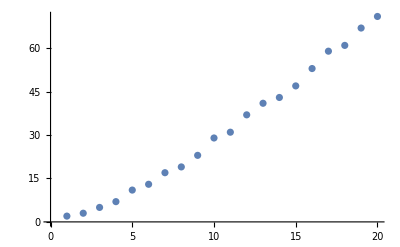

```mathematica
ListPlot[Table[Prime[i],{i,20}]]
```

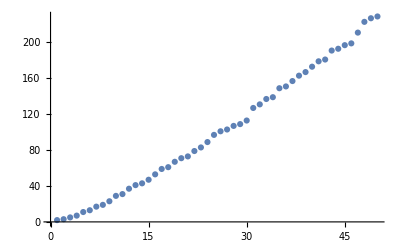

```mathematica
ListPlot[Table[Prime[i],{i,50}]]
```

```mathematica
ListPlot3D[{{1,1,1,1},{1,2,1,2},{1,1,3,1}{1,2,1,4}}, Mesh -> All, ColorFunction -> "Rainbow"]
```

-Graphics3D-

```mathematica
ListPlot3D[{{1,1,1,1},{1,2,1,2},{1,1,3,1}{1,2,1,4}}, Mesh -> None, ColorFunction -> "Rainbow"]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[Sin[i]*Cos[j],{i,-5,5},{j,-5,5}],ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[Sin[i] Cos[j],{i,-5,5},{j,-5,5}],Mesh->Automatic,MeshFunctions->Automatic,ColorFunction->"Rainbow"]
```

```mathematica
ListPlot3D[{{1,1,1,1},{1,2,1,2},{1,1,3,1}}, Mesh -> All, ColorFunction -> "Rainbow"]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[Sin[i]*Cos[j],{i,-5,5,0.25},{j,-5,5,0.25}],ColorFunction->"Rainbow"]
```

```mathematica
Show[%152,Background->Black]
```

-Graphics3D-

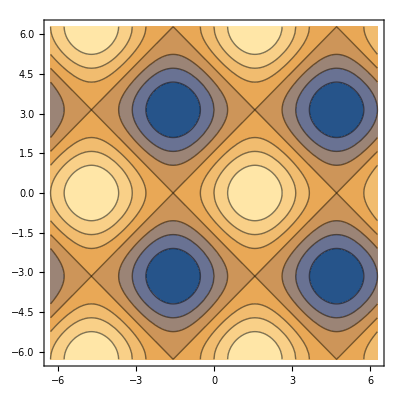

```mathematica
ContourPlot[Sin[x]+Cos[y],{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

```mathematica
ContourPlot3D[Sin[x]+Cos[y]+Sin[z],{x,-2Pi,2Pi},{y,-2Pi,2Pi},{z,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
graph1 = Plot3D[Sin[x]+Cos[y],{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
graph2 = ParametricPlot3D[{Sin[u],Sin[u]+Cos[v],Cos[v]},{u,-2Pi,2Pi},{v,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
Show[graph1,graph2]
```

Show::gcomb: Could not combine the graphics objects in Show[graph1,graph2].

```mathematica
Show[graph1,graph2]
```

-Graphics3D-

```mathematica
Show[%163,Background->Black]
```

-Graphics3D-